```mathematica
epsilon = 0.01;sheet = MeshRegion[{{0,0},{0,1},{1,0},{1,1}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}];rod = MeshRegion[{{1,0.5-epsilon},{1,0.5+epsilon},{2,0.5-epsilon},{2,0.5+epsilon}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}];
reg = RegionUnion[sheet,rod];
```

```mathematica
kk = 50;
initFunc[x_,y_]:=kk*x^2*(x-2)^2*y^2*(y-1)^2;
```

```mathematica
(*Whole region, alphaSheet for all diffusion*)
alphaSheet  = 0.02; alphaRod=0.8;
diffFunc[x_]:=Piecewise[{{alphaSheet,x<1},{alphaRod,x>1}}];
valsUniformDiffusion = NDSolveValue[{D[u[t,x,y],t]==alphaSheet*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
valsNonUniformDiffusion = NDSolveValue[{D[u[t,x,y],t]==diffFunc[x]*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
(*Manipulate[Plot3D[{valsUniformDiffusion[t,x,y],
valsNonUniformDiffusion[t,x,y],
0,3},{x,y}∈reg,
PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]

yy=0.5;Manipulate[Plot[{valsUniformDiffusion[t,x,yy],valsNonUniformDiffusion[t,x,yy],0,3},{x,0,2},PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]*)
```

```mathematica
XderivUniformDiffusion[t_,x_,y_]:=D[valsUniformDiffusion[tV,xV,yV],xV]/.{tV->t,xV->x,yV->y};
XderivNonUniformDiffusion[t_,x_,y_]:=D[valsNonUniformDiffusion[tV,xV,yV],xV]/.{tV->t,xV->x,yV->y};
```

```mathematica
YderivUniformDiffusion[t_,x_,y_]:=D[valsUniformDiffusion[tV,xV,yV],yV]/.{tV->t,xV->x,yV->y};
YderivNonUniformDiffusion[t_,x_,y_]:=D[valsNonUniformDiffusion[tV,xV,yV],yV]/.{tV->t,xV->x,yV->y};
```

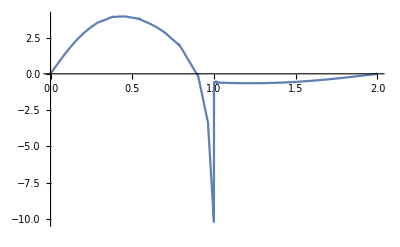

```mathematica
(*Diffusion in middle of system*)
tVV=0.4;
Plot[XderivNonUniformDiffusion[tVV,x,0.5],{x,0,2}]
```

```mathematica
(*Diffusion at borders. should be near zero*)
Table[YderivNonUniformDiffusion[tVV,x,1],{x,0,1,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0],{x,0,1,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0.5-epsilon],{x,1,2,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0.5+epsilon],{x,1,2,.1}]
```

{0.0169786,-0.019675,0.0259687,0.038313,0.0423303,-0.0069268,-0.0855265,-0.0156637,-0.0144929,-0.00279237,-0.159318}

{0.00922794,0.0195883,0.0257175,-0.00422557,-0.00929844,0.115056,0.0710429,0.0193586,0.024241,0.0126626,0.161403}

{-11.0459,-7.70344×10^-6,-0.0000202268,-0.0000324039,-0.0000573767,-0.0000347816,-8.1789×10^-6,-0.0000149082,-0.0000158384,-0.0000159607,-6.81108×10^-7}

{0.403083,-0.0000481044,-0.00003019,-0.0000213411,-9.47313×10^-6,-0.0000352655,-0.0000485396,-0.0000233327,-0.0000111446,-2.34589×10^-6,-2.45902×10^-6}

```mathematica
Table[XderivNonUniformDiffusion[tVV,0,y],{y,0,1,.1}]
Table[XderivNonUniformDiffusion[tVV,1,y],{y,0,0.5-epsilon,.1}]
Table[XderivNonUniformDiffusion[tVV,1,y],{y,0,0.5+epsilon,.1}]
Table[XderivNonUniformDiffusion[tVV,2,y],{y,0.5-epsilon,0.5+epsilon,.02}]
```

{-0.0192132,0.0165244,0.00855673,0.0135021,-0.0101677,0.0198075,-0.00444123,-0.0106503,0.0116932,0.0118408,-0.00467372}

{0.0758444,-0.0697325,-0.0659524,0.0281487,-0.1334}

{0.0758444,-0.0697325,-0.0659524,0.0281487,-0.1334,-10.2912}

{-4.31459×10^-6,-7.26761×10^-6}

```mathematica
Table[NIntegrate[valsNonUniformDiffusion[curT,x,y],{x,y}∈reg],{curT,0.1,9.1,1}]
```

{0.92222,0.92222,0.92222,0.92222,0.92222,0.92222,0.92222,0.92222,0.92222,0.92222}